```mathematica
f[x_]=Cos[5x]-12x-0.5
```

-0.5-12 x+Cos[5 x]

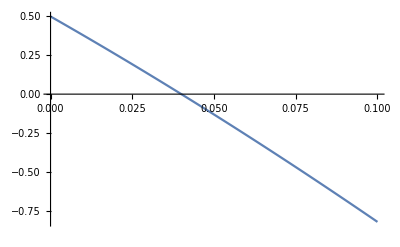

```mathematica
Plot[f[x],{x,0,0.1}]
```

```mathematica
f[0]*f[0.1]<0
```

True

```mathematica
g[x_]=(Cos[5x]-0.5)/12
```

1/12 (-0.5+Cos[5 x])

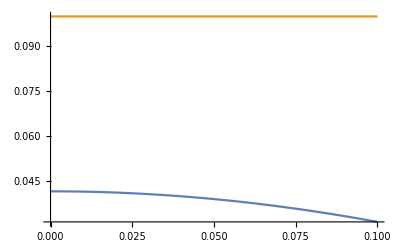

```mathematica
Plot[{g[x],0.1},{x,0,0.1}]
```

```mathematica
(*g:[0,0.1]->[0,0.1]*)
prvi[x_]=D[g[x],x]
```

-5/12 Sin[5 x]

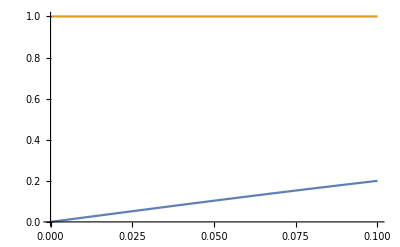

```mathematica
Plot[{Abs[prvi[x]],1},{x,0,0.1}]
```

```mathematica
iter[0]=0//N;
iter[1]=0.1;
i=1;
```

```mathematica
While[Abs[iter[i]-iter[i-1]]>=10^-6,
iter[i+1]=g[iter[i]];
i=i+1;
]
```

```mathematica
iter[i]
```

0.0400052

```mathematica
a=1;b=2;
```

```mathematica
n=20;
```

```mathematica
h=(b-a)/n//N;
```

```mathematica
res={{1,3}}
res[[1,2]]
```

{{1,3}}

3

```mathematica
f[t_,y_]=7*y+12*t*Cos[2*t];
```

```mathematica
Do[
pom=res[[i,2]]+h/2 f[res[[i,1]],res[[i,2]]];
new=res[[i,2]]+h*f[res[[i,1]]+h/2,pom];
res=Append[res,{res[[i,1]]+h,new}],
{i,1,n-1}];
```

```mathematica
res
```